## Delta potential + hard wall scattering

We have a delta potential at x = dd , that is, V(x) = - aa * delta(x - dd).

```mathematica
Remove[k, AA, UU, dd, aa]
```

```mathematica
dd := 1
aa := 1
```

```mathematica
psi1[x_] := AA * (Exp[-I * k * x] - Exp[I * k * x])
psi2[x_] := Exp[-I * k * x] + UU * Exp[I * k * x]
psi[x_] := If[x < dd,psi1[x],psi2[x]]
```

Use continuity and discontinuity of the derivative of the wave function to obtain the coefficients:

```mathematica
Solve[{
psi1[dd] == psi2[dd],
psi2'[dd] - psi1'[dd]== - aa psi1[dd]
}, {AA, UU}]
```

{{AA→-(2 k)/(ⅈ-ⅈ ⅇ^(2 ⅈ k)-2 k),UU→-(ⅇ^(-2 ⅈ k) (-1+ⅇ^(2 ⅈ k)-2 ⅈ ⅇ^(2 ⅈ k) k))/(-1+ⅇ^(2 ⅈ k)-2 ⅈ k)}}

```mathematica
AA := -(2 k)/(ⅈ-ⅈ ⅇ^(2 ⅈ k)-2 k);
```

```mathematica
UU:=-(ⅇ^(-2 ⅈ k) (-1+ⅇ^(2 ⅈ k)-2 ⅈ ⅇ^(2 ⅈ k) k))/(-1+ⅇ^(2 ⅈ k)-2 ⅈ k)
```

Plot of wavefunction:

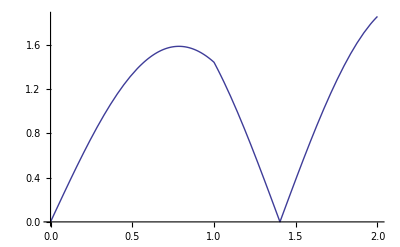

```mathematica
Plot[Abs[psi[x] /. {k -> 2}], {x, 0.0, 2.0}]
```

Plot of derivative (note the discontinuity at x = 1.0)

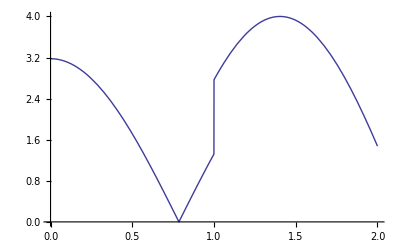

```mathematica
Plot[Abs[psi'[x]] /. {k -> 2}, {x, 0.0, 2.0}]
```

Plot of phase shift:

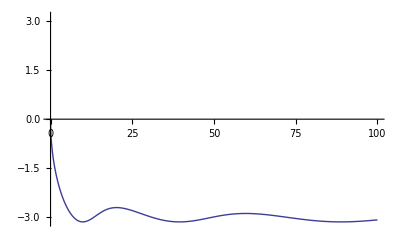

```mathematica
Plot[Arg[UU /. {k -> Sqrt[en]}], {en, 0.0,100.0}, PlotRange->{Automatic, {-Pi, Pi}}]
```